## Question 6: Mohamed Gas

x = 1 - cos (t)

y=1+sin(t)
t=π/4

Finding the Value of x

x=1-cos(t), t=π/4
x=1-cos(π/4)
x=1-(√2)/2
x=(2-√2)/2

Finding the Value of Y
y=1+sin(t)
y=1+sin(π/4)
y=1+(√2)/2
y=(2+√2)/2

derivative of dy/dx=dy/dt/dx/dt
dy/dx=dy/dt/dx/dt

y=1+Sin(t)
dy/dt=Cos(t)
x=1-Cos(t)
dx/dt=Sin(t)

dy/dx=(Cos(t))/(Sin(t))
=Cot(t)

Equation of tangenr Line 

y-((2+√2)/2)=Cot(π/4)(x-(2-√2)/2)
y=x-(2+√2)/2+(2+√2)/2
y=x+(2 √2)/2
y[x_]=x+(2 √2)/2

(d^2 y)/dx^2

dy/dx=Cot(t)
(d^2 y)/dx^2=-Csc(t)^2
(d^2 y)/dx^2=-Csc(π/4)^2
=-2

Plotting to the graph

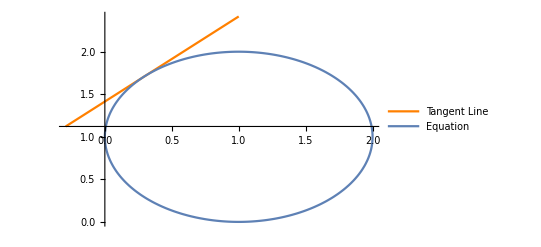

```mathematica
tangentline=Plot[x+(2 √2)/2,{x,-1+1/(√2),1},PlotRange->All,PlotStyle->Orange,PlotLegends->{"Tangent Line "}];graph=ParametricPlot[{1+Sin[t],1-Cos[t]},{t,0,2π},PlotRange->All,PlotLegends->{"Equation"}];
Show[{tangentline,graph}]
```